# mma解

```mathematica
Clear["Global`*"];
-Graphics-;
-Graphics-;
α=30°;
b=1;
NodeList={
{0,0},
{b,-b Tan[α]},
{b,b Tan[α]}
};
poly=Polygon[NodeList];
region=Region[poly];
boundary=(x==b||y==Tan[α]x||y==-Tan[α]x);
```

```mathematica
equation=∇_{x,y}^2 u[x,y]==-1;
res=NDSolveValue[{equation,DirichletCondition[u[x,y]==0,boundary]},u[x,y],{x,y}∈region];
res
```

InterpolatingFunction[…][x,y]

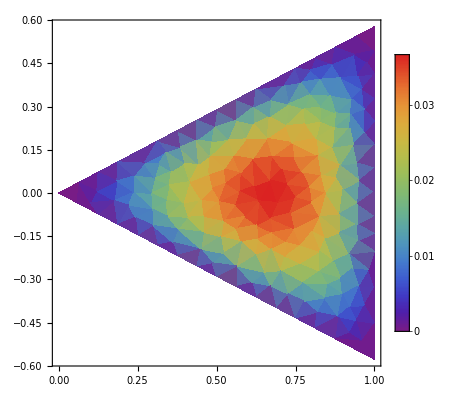

```mathematica
picture=DensityPlot[res,{x,y}∈region,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```

```mathematica
res/.{x->0.5,y->0}
```

0.0312482

```mathematica
Export["C:\\Users\\bcynuaa\\Desktop\\solution_mma.pdf",picture]
Export["C:\\Users\\bcynuaa\\Desktop\\solution_mma.png",picture]
```

C:\Users\bcynuaa\Desktop\solution_mma.pdf

C:\Users\bcynuaa\Desktop\solution_mma.png

# Mesh网格

```mathematica
mesh=TriangulateMesh[poly,MaxCellMeasure->0.00002]
```

-Graphics-

```mathematica
Export["C:\\Users\\bcynuaa\\Desktop\\mesh.ply",mesh];
```

# 公式推导

```mathematica
Clear["Global`*"];
area=Det[{
{1,x1,y1},
{1,x2,y2},
{1,x3,y3}
}]//Simplify;
ϕ1=(area/.{x1->x,y1->y})/A2//Simplify;
ϕ2=(area/.{x2->x,y2->y})/A2//Simplify;
ϕ3=(area/.{x3->x,y3->y})/A2//Simplify;
ϕ1
ϕ2
ϕ3
∇_{x,y} ϕ1
∇_{x,y} ϕ2
∇_{x,y} ϕ3
```

(x3 (y-y2)+x (y2-y3)+x2 (-y+y3))/A2

(x1 y-x3 y-x y1+x3 y1+x y3-x1 y3)/A2

(x2 (y-y1)+x (y1-y2)+x1 (-y+y2))/A2

{(y2-y3)/A2,(-x2+x3)/A2}

{(-y1+y3)/A2,(x1-x3)/A2}

{(y1-y2)/A2,(-x1+x2)/A2}

```mathematica
NodeList={
{x1,y1},
{x2,y2},
{x3,y3}
};
domain=Region[Polygon[NodeList]]
```

Region[…]

```mathematica
H[ϕi_,ϕj_]:=Integrate[Dot[∇_{x,y} ϕi,∇_{x,y} ϕj],{x,y}∈domain];
F[ϕi_]:=Integrate[ϕi,{x,y}∈domain];
```

```mathematica
K={
{H[ϕ1,ϕ1],H[ϕ1,ϕ2],H[ϕ1,ϕ3]},
{H[ϕ2,ϕ1],H[ϕ2,ϕ2],H[ϕ2,ϕ3]},
{H[ϕ3,ϕ1],H[ϕ3,ϕ2],H[ϕ3,ϕ3]}
}/.A2->Abs[area]//FullSimplify;
b={F[ϕ1],F[ϕ2],F[ϕ3]}/.A2->Abs[area]//FullSimplify;
K
b
```

{{ConditionalExpression[((x2-x3)^2+(y2-y3)^2)/(2 Abs[x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3]), ],ConditionalExpression[((x1-x3) (-x2+x3)+(y1-y3) (-y2+y3))/(2 Abs[x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3]), ],ConditionalExpression[((x1-x2) (x2-x3)+(y1-y2) (y2-y3))/(2 Abs[x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3]), ]},{ConditionalExpression[((x1-x3) (-x2+x3)+(y1-y3) (-y2+y3))/(2 Abs[x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3]), ],ConditionalExpression[((x1-x3)^2+(y1-y3)^2)/(2 Abs[x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3]), ],ConditionalExpression[-(x1^2+x2 x3-x1 (x2+x3)+(y1-y2) (y1-y3))/(2 Abs[x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3]), ]},{ConditionalExpression[((x1-x2) (x2-x3)+(y1-y2) (y2-y3))/(2 Abs[x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3]), ],ConditionalExpression[-(x1^2+x2 x3-x1 (x2+x3)+(y1-y2) (y1-y3))/(2 Abs[x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3]), ],ConditionalExpression[((x1-x2)^2+(y1-y2)^2)/(2 Abs[x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3]), ]}}

{ConditionalExpression[1/6 (x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3)), ],ConditionalExpression[1/6 (x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3)), ],ConditionalExpression[1/6 (x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3)), ]}